```mathematica
APPM 2350 Project 2: Hiking
```

## Defining the Moutain Range

```mathematica
(*creating mountain range*)
m1[x_,y_]=ⅇ^-(1*√((x-1)^2+(y-1.1)^2))^2;
m2[x_,y_]=ⅇ^-(3*√((x-3)^2+(y-2)^2))^2;
m3[x_,y_]=ⅇ^-(1*√((x-4)^2+(y-1)^2))^2;
m4[x_,y_]=ⅇ^-(2*√((x-4)^2+(y-3.5)^2))^2;
m5[x_,y_]=ⅇ^-(3*√((x-3)^2+(y-3.5)^2))^2;
m6[x_,y_]=ⅇ^-(2*√((x-2)^2+(y-3)^2))^2;
m7[x_,y_]=ⅇ^-(2*√((x-4)^2+(y-2)^2))^2;
M[x_,y_]=(1.5*m1[x,y]+0.5*m2[x,y]+0.5*m3[x,y]+1*m4[x,y]+0.75*m5[x,y]+1*m6[x,y]+0.5*m7[x,y])+7;
Mx[x_,y_] = D[M[x,y],x];
Mxx[x_,y_] = D[Mx[x,y],x];
My[x_,y_] = D[M[x,y],y];
Myy[x_,y_] = D[M[x,y],y];
Mxy[x_,y_] = D[Mx[x,y],y];
Gradm[x_,y_]=Grad[My[x,y], {x,y}];
```

## Analyzing the Mountain Range

```mathematica
x[t_]= 2.5 + 1.8*Cos[(4*t)];(*X component of trail path*)
y[t_]= 2 + 1.2*Sin[(4*t)];(*y component of trail path*)
x1[t_] = D[x[t], t];(*first derv of x*)
y1[t_] = D[y[t],t];(*first derv of y*)
r[t_]= {x[t],y[t]};(*vector equation for trail path*)
v[t_] =D[r[t], t];(*derv of vector path r(t) with respect to t*)
u[t_] = Normalize[v[t]];(*unit vector of velocity vector*)
G[t_] = Gradm[x[t], y[t]];
d[t_]= Dot[G[t],u[t] ];(*the directional derv is the gradient dotted with the directional unit tangent*)
R[t_]={x[t],y[t],M[x[t],y[t]]};(*3D plot of route*)
```

## Steepest Decent

## Slope Max and Min

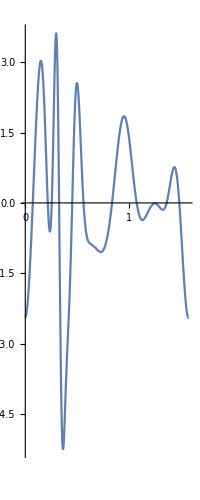

{3.61358,{t→0.296813}}

{-5.24767,{t→0.362725}}

```mathematica
ParametricPlot[{t, d[t]}, {t,0,π/2}]
FindMaximum[d[t], {t, 0.28 }](*greatest rate of change/slope*)
FindMinimum[d[t], {t, 0.38}](*least rate of change/slope*)
```

## Highest Points

```mathematica
R[x_,y_]=((x-2.5)/1.8)^2+((y-2)/(-1.2))^2-1;
Rx[x_,y_]= D[R[x,y], {x}];
Ry[x_,y_]= D[R[x,y], {y}];
FindRoot[{Mx[x,y] == λ*Rx[x,y],My[x,y] == λ*Ry[x,y],R[x,y]== 0},{x,0.9}, {y,1}, {λ, 0}]
(*height at max*)
```

```mathematica
{x->1.1109245153622094,y->1.2368284602388133,λ->0.375481758231771}
M[1.1109245153622094,1.236828460238813](*MAX Height in 1000ft*)
```

{x→1.11092,y→1.23683,λ→0.375482}

8.45429

## Honey Badger

```mathematica
(*honeybadger location*)
badger = {x[π/4],y[π/4]}(*2D*)
badger2={x[π/4],y[π/4],M[x[π/4],y[π/4]]}
(*honey badger slope*)
slope = d[π/4]
```

{0.7,2.}

{0.7,2.,7.60988}

-0.757415

## Plots

-Graphics3D-

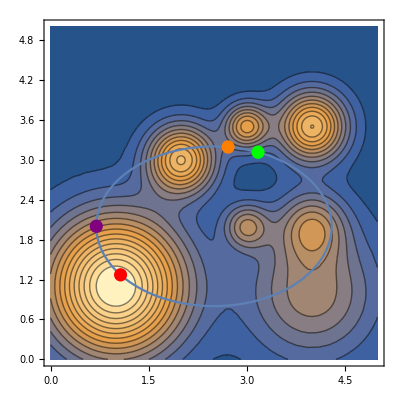

```mathematica
route = ParametricPlot[{x[t],y[t]},{t, 0, π/2}];
route3d = ParametricPlot3D[{x[t],y[t], M[x[t],y[t]]},{t, 0, π/2}];
mountains = Plot3D[M[x,y],{x,0,5},{y,0,5}];
test  = ContourPlot[M[x,y], {x,0,5},{y,0,5}, Contours->15];
Show[mountains, route3d,Point1,Point5,Point8,Point10,PlotRange-> All]
Show[test, route,Point2,Point6,Point7,Point9, PlotRange -> All]
```

```mathematica
Point5=Graphics3D[Sphere[{.7,2,7.60988},.14]];
```

```mathematica
R[π/4]
```

{0.7,2.,7.60988}

```mathematica
Point6=Graphics[{Purple,Disk[{.7,2},.1]}];
```

```mathematica
R[0.29681314113038754]
```

{3.17358,3.11281,7.19133}

```mathematica
Point7=Graphics[{Green,Disk[{3.17358,3.11281},.1]}];
```

```mathematica
Point8=Graphics3D[Sphere[{3.1735763803082557,3.1128132237992996,7.191328906234793},.14]];
```

```mathematica
Point9=Graphics[{Orange,Disk[{2.71529,3.19139},.1]}];
```

```mathematica
R[0.3627253269042548]
```

{2.71529,3.19139,7.26774}

```mathematica
Point10=Graphics3D[Sphere[{2.7152943653727446,3.1913854374427086,7.2677359632528775},.14]];
```